argument:

Abs[⟨1|dH/dB|0⟩]/Gap^2 dB/dt<<1

∫Abs[⟨1|dH/dB|0⟩]/Gap^2 dB=∫dt

for two dimensions, this is replaced by

Abs[ ⟨1|dH/dB|0⟩dB +  ⟨1|dH/dA|0⟩dA]/Gap^2=dt

This is the local time cost

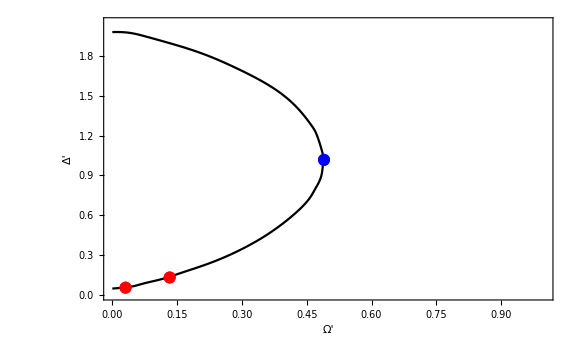
```mathematica
g1=-Graphics-;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Library/Mobile Documents/com~apple~CloudDocs/Research_projects/0.0 Rydberg_Atoms/adiabatic_ramping

```mathematica
(*DumpSave["curves.md",curves];*)
```

```mathematica
<<"curves.md"
```

```mathematica
{{0,1},{1,0},{1,1},{1,2},{2,1},{1,4},{4,1}};
Line[{{0,0},#}]&/@%;
Graphics[{Cyan,Rectangle[{0,0},{4,4}],Black,%}]
```

-Graphics-

```mathematica
π/2//N
```

1.5708

```mathematica
g2=ListPlot[curves,Joined->True,PlotStyle->{Red,Green,Cyan,Blue,Pink,Magenta,Cyan},AspectRatio->3/2];
```

```mathematica
temp0="{{"~StringJoin~(Import["vectors.txt","String"]//StringReplace[#,"
"->"},{"]&)~StringJoin~"}}"//ToExpression;
temp0=temp0[[1;;Length[temp0]-1]];
```

ArcTan[⟨ψ0|H3|ψ1⟩/⟨ψ0|H2|ψ1⟩]

H2: Σ X
H3: Σ n

```mathematica
Show[ListContourPlot[{#[[1]],#[[2]],(*1/π Mod[ArcTan[(#[[5]])/(#[[4]])],π]*)ArcTan[(#[[5]])/(#[[4]])]}&/@temp0,Contours->Table[(2π)/40 i-π,{i,0,40}],PlotLegends->Automatic,PlotRange->{{0,2},{-2,1}},ImageSize->Large],g1,g2]
```

The discontinuity, could it be because of level crossing??? 
Indeed!!! But this can be worked out.

```mathematica
(*Show[g2,g1,ListPlot[curvepart1~Join~curvepart2[1],PlotStyle->Red,Joined->True],ListPlot[{#[[1]]-0.005,#[[2]]-0.005}&/@(curvepart1~Join~curvepart2[2]),PlotStyle->Blue,Joined->True],ImageSize->Large,FrameLabel->{"Ω","Δ"},FrameStyle->{Directive[15],Directive[15]}]*)
```

```mathematica
g3=ListContourPlot[{#[[1]],#[[2]],#[[3]]}&/@temp0,Contours->20,PlotLegends->Automatic,PlotRange->{{0,2},{-1.47,1}}];
```

```mathematica
Show[g3,g1,g2,ListPlot[{{0,-0.5}},PlotStyle->{Cyan,PointSize[0.03]}],ImageSize->Large]
(*Cyan=12.49483409647097,Green=3.567030080677229,Red=2.9715028177548963*)
```

-Graphics-

```mathematica
{{0.6594,0.6624}-{0.1297,0.129}}
```

{{0.5297,0.5334}}

### Energy levels at some points

{Ω,Δ}= {0.1248, -0.488}:

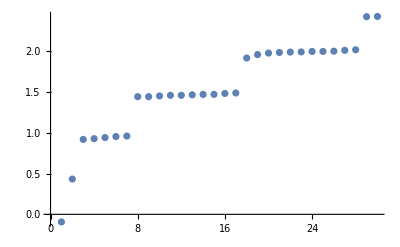

```mathematica
ListPlot[{-0.09276340260553373,0.43221636242380973,0.9179687952845942,0.9268878331121816,0.94018738003743,0.9529858756671803,0.9586024837788362,1.4412330115429537,1.4413309830046726,1.4499494468937957,1.4579203719321376,1.4582981968795947,1.4641535535646846,1.4689094474760955,1.4694502760196828,1.4806827679434282,1.4864225921842582,1.914991326742719,1.9570723924414237,1.975517637049098,1.983100569903161,1.9876192857652035,1.9895916580387014,1.9951141836077053,1.9955436471298336,1.9987556092217618,2.0089667079282942,2.0158194183220943,2.4210906468560043,2.42393695266039}]
```

Ω=1.139, Δ=-0.1729:

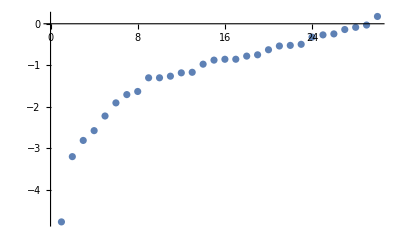

```mathematica
ListPlot[{-4.780935504275626,-3.20609235996453,-2.8154094666389713,-2.5788798646884405,-2.2256187651709407,-1.9090232016745057,-1.7090865951541023,-1.6337410548531108,-1.3040130457318257,-1.3038113017363404,-1.264905742259081,-1.1842801319260827,-1.170814623418794,-0.9751681709976207,-0.8771428795479553,-0.8565765085665374,-0.8557463582602954,-0.780272040082072,-0.7490390608760833,-0.627074666384853,-0.5363296222769384,-0.5220419040975117,-0.4957451751721802,-0.3221217455797519,-0.26847363666767216,-0.2447637150325962,-0.13898845956710365,-0.08581749240311866,-0.03087490244247826,0.17631600630820043}]
```

Ω=0.887, Δ=0.6524:

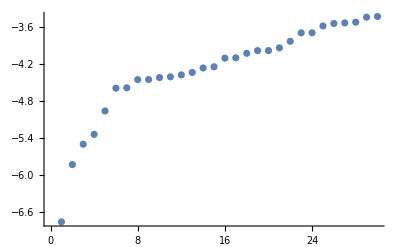

```mathematica
ListPlot[{-6.766554154946617,-5.836193843141175,-5.506132212077785,-5.346048964542332,-4.966607684720792,-4.596769172558825,-4.590017034656901,-4.457787579701558,-4.456732742155323,-4.424012985468382,-4.412712032943047,-4.380812325422607,-4.34143786281904,-4.269422063684467,-4.249245979574657,-4.1089260105113885,-4.10338482219399,-4.031114192108499,-3.9867932319734605,-3.9864497884505266,-3.942259031481532,-3.8356002982760904,-3.6990035802982737,-3.697875160239485,-3.586752361965822,-3.5467370473792035,-3.5376503765868943,-3.5252640039179526,-3.4442526769610153,-3.4326519442642525}]
```

{{0.9254, 0.2133}}
Close to the “level crossing”

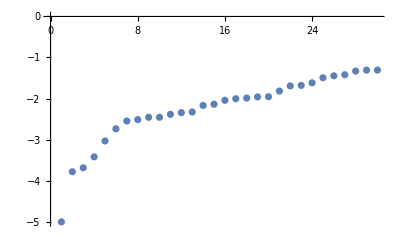

```mathematica
ListPlot[{-5.007597235196678,-3.7847069342423616,-3.6879743808957426,-3.4223213098766188,-3.035845966681254,-2.738802333476459,-2.5484133983030675,-2.5147136200830813,-2.4575900527736305,-2.4570852268967927,-2.3852862482436974,-2.3441908394303463,-2.3290123851043183,-2.168983269247134,-2.1396412317876456,-2.0440731977561417,-2.0052880837791403,-1.9887754080083084,-1.960650241015067,-1.9553039438918962,-1.817885117532316,-1.6928860598407631,-1.6804517249526612,-1.6167846406941297,-1.4937656604116267,-1.446470220533043,-1.4206264060684302,-1.3314547238121983,-1.308333322180394,-1.306402352785324}]
```